Quartic Covariant Galileon

```mathematica
Quit[]
```

```mathematica
?NSolve
```

NSolve[expr,vars] attempts to find numerical approximations to the solutions of the system expr of equations or inequalities for the variables vars. 
NSolve[expr,vars,Reals] finds solutions over the domain of real numbers.

```mathematica
(*OmegaM0=0.293;
OmegaR0=10^(-5);
OmegaPhi0=1-OmegaM0-OmegaR0*)
OmegaM0=0.293
OmegaR0=8.32*10^(-5)(*10^(-5)*)(*8.32*10^(-5)*)
OmegaPhi0=1-OmegaM0-OmegaR0
s=1
a=.
HoverH0equation=1-x^-2(OmegaM0/a+OmegaR0/a^2)-(a/x)^(2(1+s))(OmegaPhi0); (*x is conformal H over H_0*)
Solution=NSolve[HoverH0equation==0,x]
a=1
Solution (*Looking at this I know the right solution is the fourth one*)
```

0.293

0.0000832

0.706917

1

{{x→-7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a-(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)},{x→7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a-(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)},{x→-7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a+(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)},{x→7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a+(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)}}

1

{{x→0.-0.840783 ⅈ},{x→0.+0.840783 ⅈ},{x→-1.},{x→1.}}

```mathematica
0.00223606797749979 √(1/a^2+29300./a+(√(1.+58600. a+8.5849*^8 a^2+2.82796*^10 a^8))/a^2)
```

```mathematica
{{x->-7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a-(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2)},{x->7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a-(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2)},{x->-7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a+(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2)},{x->.03}}
```

1

{{x→0.-0.840783 ⅈ},{x→0.+0.840783 ⅈ},{x→-1.},{x→1.}}

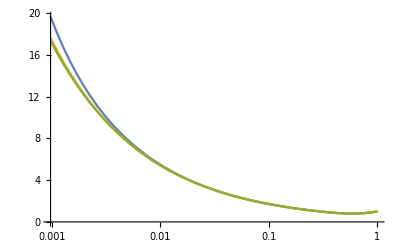

```mathematica
LogLinearPlot[{7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a+(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2),0.00223606797749979 √(1/a^2+29300./a+(√(1.+58600. a+8.5849*^8 a^2+2.82796*^10 a^8))/a^2),0.022360679774997897 √(293./a+(√(85849.+2.828*^6 a^6))/a)},{a,0,1}]
```

```mathematica
a=.
HconfOverH0=7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a+(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2)
HLCDM = Sqrt[OmegaM0/a+OmegaR0/a^2+a^2 *OmegaPhi0]
```

7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a+(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)

√(0.0000832/a^2+0.293/a+0.706917 a^2)

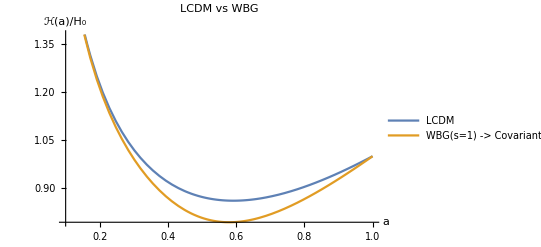

```mathematica
Plot[{HLCDM,HconfOverH0},{a,0.1,1}, PlotLegends->{"LCDM","WBG(s=1) -> Covariant Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/H_0",FontSize->20]},PlotLabel->Style["LCDM vs WBG", FontSize->30]]
```

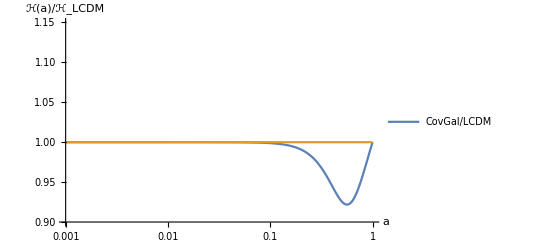

```mathematica
LogLinearPlot[{ HconfOverH0/HLCDM,HLCDM/HLCDM },{a,0.001,1}, PlotLegends->{"CovGal/LCDM"}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/ℋ_LCDM",FontSize->20]},PlotLabel->Style[" ", FontSize->30], PlotRange->{{0.001,1},{0.9,1.15}}]
```

Let’s find X(a)

```mathematica
XoverXds = (   (1-OmegaM0-OmegaR0)^( 1/(2(s+1)) ) HconfOverH0^(-1) a )^(1/q)/.p->1/.q->1/2//PowerExpand//Simplify
```

(1.3688×10^16 a^4)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))

```mathematica
(*XLCDM = 
Xs0 =69998.99999999997 (a^2/(√(1.+30000. a+69999. a^4)))^2.
Xs0p5 =0.7883660079734442 (a/(-(1.2599210498948732 (-1.-30000. a))/((1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3))+1/a^2 2.645668419946999*^-6 (1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3)))^2.
Xsm0p5=1.9599440004000008*^10 (a^3/(69999. a^3+√(-400000. (-1.-30000. a) a^2+4.899860001*^9 a^6)))^2.
Xs1 = 167330.81007393703 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^2.
Xs1o5 = 10.824004689806106 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^(2/5)*)
```

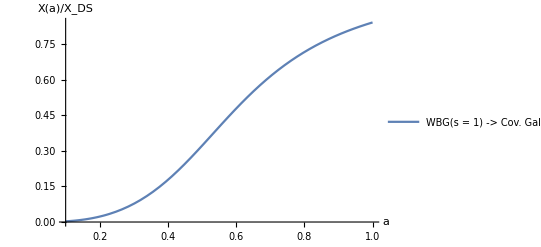

```mathematica
Plot[{XoverXds},{a,0.1,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Χ(a)/Χ_DS",FontSize->20]}]
```

lets calculate Phi prime (derivative of phi w.r.t. scale factor a)

```mathematica
Sqrt[-XoverXds Xds]/HconfOverH0//PowerExpand//Simplify
```

((0.+1.49278×10^16 ⅈ) √(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)) √Xds)/(((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)^(3/2))

EFT functions plots

Covariant Galileon

```mathematica
p=.
q=.
s=.
CovGal = {s->1,p->1, q->1/2}
```

{s→1,p→1,q→1/2}

```mathematica
c4=.
c5=0;
DeSitterFP = {Subscript[c, 2]->3-6 Subscript[c, 4]-24 Subscript[c, 5]+12 Subscript[c, 4] p+24 Subscript[c, 4] q,Subscript[c, 3]->(√2 p)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] p)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] p)/(-1+2 p+2 q)+(8 √2 Subscript[c, 4] p^2)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] q)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] q)/(-1+2 p+2 q)+(24 √2 Subscript[c, 4] p q)/(-1+2 p+2 q)+(16 √2 Subscript[c, 4] q^2)/(-1+2 p+2 q)}
```

{c_2→3-6 c_4+12 c_4 p+24 c_4 q,c_3→(√2 p)/(-1+2 p+2 q)-(4 √2 c_4 p)/(-1+2 p+2 q)+(8 √2 c_4 p^2)/(-1+2 p+2 q)-(4 √2 c_4 q)/(-1+2 p+2 q)+(24 √2 c_4 p q)/(-1+2 p+2 q)+(16 √2 c_4 q^2)/(-1+2 p+2 q)}

Let’s find the values for c4 and Xds from Simone’s paper

```mathematica
Solve[{Xds==(2 (3+6 d4-24 c5+12 d4 p) Hds^2M^2)/(c2),d4==-(c4 Xds^2)/(4M^4 H0^4)},{Xds,d4}]/.Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)/.p->1/.q -> 1/2/.c5->0/.c2->-1/.c4->-1/9 xi^(-2)+2/3(1-OmegaM0-OmegaR0) xi^(-4)/.xi->2.53//FullSimplify;
%/.√(H0^8)-> H0^4
```

{{Xds→-14.9535 H_0^2 M^2,d4→0.327367},{Xds→-7.61302 H_0^2 M^2,d4→0.084852}}

Common substitutions:

```mathematica
Hc=HconfOverH0 H0//Simplify
HcP = D[Hc,a]//Simplify
HcPP = D[HcP,a]//Simplify
X = XoverXds Xds//Simplify
PhiP = Sqrt[-X]/Hc//Simplify
PhiPP = D[PhiP,a]//Simplify
PhiPPP = D[PhiPP,a]//Simplify
(*adot = Hc a//Simplify
adotdot = Hc a^2 HcP + Hc adot//Simplify*)
```

7.83741×10^-9 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H_0

(3.91871×10^-9 (-1.3545×10^12-2.38502×10^15 a+(a (1.41536×10^22+4.9844×10^25 a+6.56698×10^27 a^7))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))-228246. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)) H_0)/(a^3 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2))

((2.6332×10^31+5.34856×10^48 a^5+1.05701×10^51 a^11+6.5908×10^48 a^16+1.16052×10^52 a^17+4.43719×10^24 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a (4.17292×10^35+5.46916×10^28 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (2.57172×10^39+2.40755×10^32 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (4.84036×10^40+7.25019×10^33 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (7.61908×10^42+4.36037×10^35 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (4.2615×10^44+3.82988×10^37 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (1.06314×10^46+2.55927×10^38 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (1.20059×10^48+4.63631×10^40 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) H_0)/(a^4 (3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)) √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2))

(1.3688×10^16 a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))

(1.49278×10^16 √(-(1. a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/(√((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H_0)

(5.89536×10^-21 a^3 (-3.30216×10^59-3.38598×10^73 a^4-5.57632×10^74 a^10+4.59177×10^75 a^16-5.56446×10^52 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^3 (-4.32666×10^70-1.62018×10^63 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (-7.86859×10^67-1.89419×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (-2.04766×10^67-1.61023×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (-4.26397×10^63-5.22559×10^56 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (-4.35447×10^71+4.3845×10^48 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) Xds)/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^4 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H_0 √(-(1. a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))

-((1. a^2 (2.29249×10^74-7.86338×10^107 a^15-5.18003×10^109 a^21-6.78918×10^110 a^27-7.02471×10^110 a^33+3.86306×10^67 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^26 (-7.27738×10^107-1.03751×10^100 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (-8.34745×10^106-1.73504×10^99 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^14 (-1.6821×10^105-4.26429×10^97 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^25 (-2.4706×10^104-8.50026×10^96 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (-5.25581×10^103-2.31677×10^96 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (-1.5048×10^102-7.97759×10^94 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (-2.70202×10^100-1.56344×10^93 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (-1.62488×10^100-1.12421×10^93 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (-7.32175×10^98-6.06779×10^91 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (-2.47538×10^96-2.36939×10^89 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (-2.09612×10^95-2.41221×10^88 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (-1.49029×10^92-1.83982×10^85 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (-3.53256×10^91-5.30034×10^84 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (6.36627×10^105-6.11294×10^80 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (6.45865×10^78+9.52301×10^71 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (8.05552×10^82+1.02207×10^76 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (5.8406×10^86+6.24261×10^79 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (2.71504×10^90+2.37667×10^83 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (8.40241×10^93+5.78909×10^86 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (1.7346×10^97+8.84258×10^89 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (2.30998×10^100+7.78508×10^92 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (1.80776×10^103+3.04625×10^95 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^32 (-5.31928×10^107+1.12044×10^100 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) Xds)/((3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^7 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H_0 √(-(1. a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)))))

```mathematica
CGSubstitute = {s->1,p->1, q->1/2,Subscript[χ, DS]->Xds,Hconf[a]->Hc,ℋ'[a]->HcP,ℋ''[a]->HcPP, PhiPrime[a]-> PhiP, PhiPrimePrime[a]->PhiPP,PhiPrimePrimePrime[a] ->PhiPPP,OverDot[ȧ]->adotdot, ȧ->adot,Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)};
```

```mathematica
ℋ'[a]/.CGSubstitute
ℋ''[a]/.CGSubstitute
```

0.0000832

#### Omega

```mathematica
Omega=-1-2 (-1)^(-p (1+1/s)) Subscript[c, 4] Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s)
```

-1-2 (-1)^(-p (1+1/s)) c_4 χ_DS^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s)

```mathematica
OmegaCG=Omega/.DeSitterFP/.CGSubstitute//PowerExpand//Simplify
```

-1-(3.74721×10^32 a^8 c_4)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)

```mathematica
OmegaCG1=OmegaCG/.c4->0.08485200961571562
OmegaCG2=OmegaCG/.c4-> 0.32736735291927577(*RULED OUT BY EFTCAMB COMPARISON!*)
```

-1-(3.17958×10^31 a^8)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)

-1-(1.22671×10^32 a^8)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)

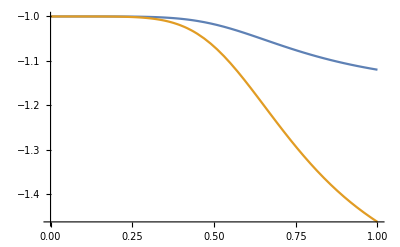

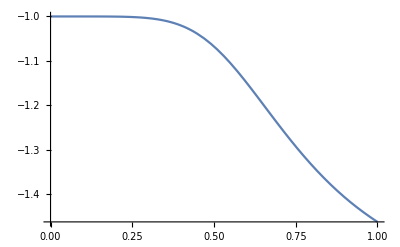

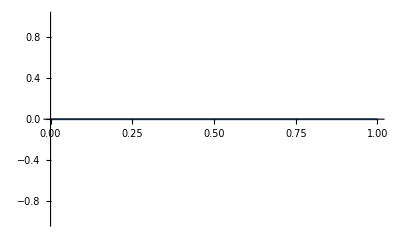

```mathematica
Plot[{Re[OmegaCG1],Re[OmegaCG2]},{a,0,1}]
Plot[Re[OmegaCG2],{a,0,1}]
Plot[Im[OmegaCG1],{a,0,1}]
```

#### Lambda

```mathematica
LEFT=1/(s^2 φ'[a]^6)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) ((-1)^(1+p+p/s) ⅈ^(p/s) a^2 Subscript[c, 2] Subscript[H, DS]^2 s^2 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(6+2 p)-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(5+p (2+1/s)) φ''[a]+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) φ'[a]^((2 p (1+s))/s) (Subscript[c, 4] p s (1+s) φ'[a]^6+a^2 Subscript[c, 4] p (1+s) (-s+2 p (1+s)) φ'[a]^4 φ''[a]^2+a φ'[a]^5 (4 Subscript[c, 4] p^2 (1+s)^2 φ''[a]+a Subscript[c, 4] p s (1+s) φ'''[a]))-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(6+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 Subscript[c, 4] p^2 (1+s)^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(6+(2 p (1+s))/s) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(5+(2 p (1+s))/s) (a Subscript[c, 4] p (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (2 Subscript[c, 4] p (1+s) (s+2 p (1+s)) ℋ'[a]+a Subscript[c, 4] p s (1+s) ℋ''[a])))
```

1/(s^2 φ'[a]^6)(-1)^(-p (2+1/s)) ⅈ^(-p/s) χ_DS^(-p (2+3/(2 s))) ((-1)^(1+p+p/s) ⅈ^(p/s) a^2 c_2 H_DS^2 s^2 χ_DS^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(6+2 p)-√2 a^2 c_3 ⅇ^((ⅈ p π (1+s))/s) H_DS s (p-s+2 p s) χ_DS^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(5+p (2+1/s)) φ''[a]+4 (-1)^p ⅈ^(p/s) χ_DS^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) φ'[a]^((2 p (1+s))/s) (c_4 p s (1+s) φ'[a]^6+a^2 c_4 p (1+s) (-s+2 p (1+s)) φ'[a]^4 φ''[a]^2+a φ'[a]^5 (4 c_4 p^2 (1+s)^2 φ''[a]+a c_4 p s (1+s) φ'''[a]))-√2 a^2 c_3 ⅇ^((ⅈ p π (1+s))/s) H_DS s (p-s+2 p s) χ_DS^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(6+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 c_4 p^2 (1+s)^2 χ_DS^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(6+(2 p (1+s))/s) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a χ_DS^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(5+(2 p (1+s))/s) (a c_4 p (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (2 c_4 p (1+s) (s+2 p (1+s)) ℋ'[a]+a c_4 p s (1+s) ℋ''[a])))

```mathematica
(*L/.MPlanck->Ee/.Xds->Ee^4/.Hconf[a]->Ee/.PhiPrime[a]->Ee/.PhiPrimePrime[a]->Ee/.PhiPrimePrimePrime[a]->Ee/.Xds->Ee^4/.Hds->Ee/.DeSitterFP/.c4->1/.p->1/.q->1/2/.Hconfdot[a]->Ee^2/.Hconfdotdot[a]->Ee^3/.OverDot[ȧ]->Ee^2/. ȧ->Ee/.a->1*)
```

```mathematica
LCGeft=LEFT/.DeSitterFP/.CGSubstitute/.c4->0.08485200961571562/.Xds->-7.613018601091973 Subscript[H, 0]^2 M^2//Simplify
```

a H_0^2 ((7.81223×10^15 a^5 (-1.3545×10^12-2.38502×10^15 a+(a (1.41536×10^22+4.9844×10^25 a+6.56698×10^27 a^7))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))-228246. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^3)-(5.21034×10^16 a^5)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+(1.8302×10^34 a^5 (-3.82388×10^40-2.69818×10^73 a^15+1.38399×10^75 a^21+3.57264×10^76 a^27+1.15499×10^77 a^33-6.4436×10^33 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^14 (-7.64044×10^70-3.407×10^62 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (-3.5215×10^69-5.77073×10^61 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (-8.67224×10^67-1.32388×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (-4.53377×10^66-1.52116×10^59 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (-5.23402×10^64-1.54708×10^57 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (-3.3808×10^63-1.73745×10^56 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (-1.8371×10^61-8.4577×10^53 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (-1.61037×10^60-1.12434×10^53 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (-3.77893×10^57-2.41913×10^50 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (-5.08448×10^56-4.51292×10^49 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (-1.20601×10^72-3.5224×10^46 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (-1.06468×10^53-1.15143×10^46 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (-1.42643×10^49-1.82487×10^42 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (-1.11001×10^45-1.64355×10^38 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (7.97587×10^55+3.01442×10^50 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (1.35425×10^61+4.91905×10^54 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (1.68828×10^65+2.8592×10^58 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (9.02949×10^65+7.49012×10^58 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (8.10775×10^68+7.10265×10^61 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^25 (9.45351×10^69+4.79214×10^62 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (1.73366×10^72+6.40089×10^64 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^32 (4.37291×10^73+1.60191×10^65 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^26 (3.22384×10^73+7.38028×10^65 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/((3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^7)+(a^5 (1.63371×10^89+1.24714×10^131 a^23+3.50983×10^131 a^29-7.78733×10^132 a^35-2.46801×10^133 a^41+2.75295×10^82 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^34 (-7.13538×10^129-1.61342×10^122 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^40 (-9.01046×10^129-8.43526×10^121 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^28 (6.75506×10^128-8.39723×10^120 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^33 (-2.09736×10^126-1.06173×10^119 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^27 (5.09413×10^125-8.30149×10^117 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^32 (-1.98522×10^122-1.67264×10^115 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^26 (1.87512×10^122-2.58298×10^114 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^25 (3.37224×10^118-2.27871×10^110 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (6.01123×10^93+9.15999×10^86 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (1.00432×10^98+1.36979×10^91 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (1.0057×10^102+1.2123×10^95 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (6.70647×10^105+7.03176×10^98 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (3.12706×10^109+2.79307×10^102 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (9.02184×10^127+3.60486×10^103 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (6.23074×10^129+6.08043×10^103 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (1.04031×10^113+7.69401×10^105 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (2.37594×10^114+8.08826×10^105 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (2.11836×10^114+1.462×10^107 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (8.2452×10^114+4.72094×10^107 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (2.46926×10^116+1.45139×10^109 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (6.93656×10^117+3.78703×10^110 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (4.37242×10^118+1.94576×10^111 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (4.09803×10^119+1.79433×10^112 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^14 (1.51177×10^121+6.11906×10^113 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (1.38709×10^122+4.49203×10^114 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (4.529×10^122+1.31283×10^115 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^15 (2.11473×10^124+5.63962×10^116 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (2.99982×10^125+4.31693×10^117 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^21 (2.63303×10^125+5.51262×10^117 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (1.723×10^127+2.27045×10^119 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^22 (2.77034×10^128+2.81382×10^120 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/((3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^9)+((0.+2.29736×10^-20 ⅈ) a^6 (-3.30216×10^59-3.38598×10^73 a^4-5.57632×10^74 a^10+4.59177×10^75 a^16-5.56446×10^52 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^3 (-4.32666×10^70-1.62018×10^63 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (-7.86859×10^67-1.89419×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (-2.04766×10^67-1.61023×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (-4.26397×10^63-5.22559×10^56 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (-4.35447×10^71+4.3845×10^48 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) √(-H_0^2 M^2))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^4 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) √((a^4 H_0^2 M^2)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))+((0.+2.90861×10^16 ⅈ) (-8.03811×10^18-4.9844×10^25 a^2+3.28349×10^27 a^8-1.3545×10^12 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a (-4.24609×10^22-2.38502×10^15 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) √((a^4 H_0^2 M^2)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8) ((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)^(3/2) √(-H_0^2 M^2)))

```mathematica
a=1
LCGeft/.√(-Subscript[H, 0]^2 M^2)-> ⅈ √(Subscript[H, 0]^2 M^2)/.√(Subscript[H, 0]^2 M^2)->ⅈ √(-Subscript[H, 0]^2 M^2)
a=.
```

1

(-5.66893+0. ⅈ) H_0^2

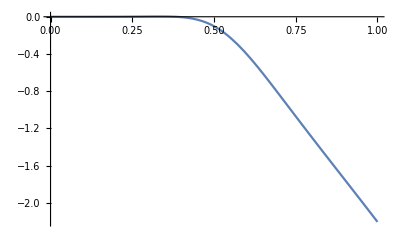

```mathematica
Plot[LCGeft,{a,0,1}]
```

```mathematica
dataEFTCAMB=Import[FileNameJoin[{NotebookDirectory[],"QuarticGalileon_BackgroundEFT.dat"}]]
```

{{1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00010001,0.,0.,-9.58378×10^-26,-7.1621×10^-21,-4.59973×10^-16,-2.46485×10^-11,2.48833×10^-28,2.11744×10^-29,9.6274×10^-28,8.41109×10^-29},{0.00020002,0.,0.,-1.54089×10^-23,-5.52218×10^-19,-1.68443×10^-14,-4.22713×10^-10,9.42325×10^-27,4.07525×10^-28,3.96389×10^-26,1.80036×10^-27},29995,{1.×10^-10,0.,0.,-1.75374×10^-73,-1.40299×10^-62,-9.82093×10^-52,-5.89256×10^-41,5.04184×10^-64,4.33759×10^-59,1.76464×10^-63,1.51816×10^-58},{1.×10^-10,0.,0.,-1.75374×10^-73,-1.40299×10^-62,-9.82093×10^-52,-5.89256×10^-41,5.04184×10^-64,4.33759×10^-59,1.76464×10^-63,1.51816×10^-58}}
 |  |  |  |

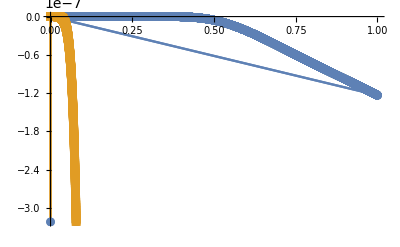

```mathematica
ListPlot[
{dataEFTCAMB⟦All,{1,10}⟧,data⟦All,{1,4}⟧}
,Joined->True
,PlotMarkers->Automatic
]
```

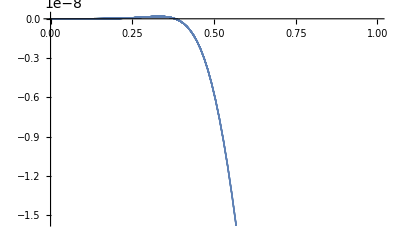

```mathematica
ListPlot[data⟦All,{1,10}⟧]
```

```mathematica
L3=L/.Phi'[a]-> Sqrt[-XoverXds Xds]/(HconfOverH0 H0)/.ȧ-> ℋ[a]a/.ℋ̇[a]-> Hconfdot[a]/.Hconfdot[a]-> D[ ℋ[a],a] ℋ[a]a/.Hconfdotdot[a]-> a^2 ℋ[a]^2 D[ D[ ℋ[a],a],a]+D[ ℋ[a],a]^2 ℋ[a]a^2+D[ ℋ[a],a]ℋ[a]^2a/.Hconf[a]->HconfOverH0 H0/.PhiPrime[a]->Sqrt[-XoverXds Xds]/(HconfOverH0 H0)/.PhiPrimePrime[a]->D[Sqrt[-XoverXds Xds]/(HconfOverH0 H0),a]/.PhiPrimePrimePrime[a]->D[D[Sqrt[-XoverXds Xds]/(HconfOverH0 H0),a],a]/.p->1/.q->1/2/.Hconf'[a]->D[HconfOverH0 H0,a]/.Hconf[a]->HconfOverH0 H0//PowerExpand//Simplify
```

1/(a^2 Xds^2 ȧ Phi'[a]^4)MPlanck^2 (-2 ⅈ √2 a (1/(√2)+9 √2 c4) Hds √Xds Hconf[a]^2 Hconfdot[a] ȧ PhiPrime[a]^3 Phi'[a]^4-2 ⅈ √2 a^2 (1/(√2)+9 √2 c4) Hds √Xds Hconf[a]^4 ȧ PhiPrime[a]^2 PhiPrimePrime[a] Phi'[a]^4+a^2 (3+18 c4) Hds^2 Xds Hconf[a]^2 ȧ Phi'[a]^6+8 c4 Hconf[a]^3 (Hconfdotdot[a] ȧ+Hconfdot[a] OverDot[ȧ]) PhiPrime[a]^2 Phi'[a]^6+8 c4 Hconf[a]^2 Hconfdot[a]^2 ȧ PhiPrime[a]^2 Phi'[a]^4 (2 PhiPrime[a]^2+Phi'[a]^2)+4 Hconf[a]^4 Hconfdot[a] ȧ PhiPrime[a] Phi'[a]^4 (8 c4 PhiPrime[a]^3+8 a c4 PhiPrime[a]^2 PhiPrimePrime[a]+10 c4 PhiPrime[a] Phi'[a]^2+10 a c4 PhiPrimePrime[a] Phi'[a]^2)+4 Hconf[a]^6 ȧ Phi'[a]^4 (8 a c4 PhiPrime[a]^3 PhiPrimePrime[a]+2 a^2 c4 PhiPrimePrime[a]^2 Phi'[a]^2+2 a c4 PhiPrime[a] (4 PhiPrimePrime[a]+a PhiPrimePrimePrime[a]) Phi'[a]^2+2 c4 PhiPrime[a]^2 (2 a^2 PhiPrimePrime[a]^2+Phi'[a]^2)))

1/a^8 MPlanck^2 (-(165999. a^12 (3+18 c4) Hds^2)/(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-(2.81158×10^16 a^7 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) (6.99909×10^-15+0.140492 a^3+1. a^9+6.99909×10^-15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^8 (0.000064288-0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (5.80644×10^-10+3.62903×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (0.0000158059+4.51596×10^-6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) (0.0555556+1. c4) H0 Hds X[a])/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^(5/2) Xds)+(1252.15 a^2 (0.000064288+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (3.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) (0.0555556+1. c4) H0 Hds X[a]^(3/2))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) Xds^(3/2))+(189.049 (3.62903×10^-11+1.69349×10^-6 a+0.0175614 a^2-1. a^8+3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+5.64495×10^-7 a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 c4 H0^2 X[a] (1. a^6 Xds+(0.0000120483+0.374822 a+0.0000120483 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) X[a]))/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 Xds^2)-(4.94985×10^19 (-3.62903×10^-11-0.0175614 a^2+1. a^8-3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (-1.69349×10^-6-5.64495×10^-7 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) c4 H0^2 √X[a] (a^9 (-1.63963×10^-15-0.0329121 a^3-0.234264 a^9-1.63963×10^-15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-3.70274×10^-6-1.05793×10^-6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.36024×10^-10-8.50149×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-0.0000150604+7.53018×10^-6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) Xds^(3/2)+a^6 √(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-1.34144×10^-18-0.0000403899 a^3-0.00114996 a^9-1.34144×10^-18 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^8 (-3.69643×10^-8-1.84822×10^-8 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-3.89488×10^-9-1.29829×10^-9 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.25197×10^-13-8.34647×10^-14 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) Xds √X[a]+a^3 (-1.58038×10^-20-0.00986893 a^4-0.0000124189 a^9-0.140492 a^10+1. a^16-1.58038×10^-20 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^3 (-1.42752×10^-6-3.17227×10^-7 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.54032×10^-10-3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-7.64771×10^-11-3.56893×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.80274×10^-15-1.31108×10^-15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) √Xds X[a]+√(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-1.29297×10^-23-0.0000121112 a^4-0.00043103 a^10-0.00245441 a^16-1.29297×10^-23 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^9 (-2.77101×10^-8-8.31302×10^-9 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^3 (-1.55721×10^-9-3.89303×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-4.45356×10^-13-2.67214×10^-13 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-7.50826×10^-14-3.75413×10^-14 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.60897×10^-18-1.20673×10^-18 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) X[a]^(3/2)))/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^(7/2) Xds^2)+(1.71581×10^-38 a^3 c4 H0^2 (5.38046×10^37 a^9 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-2.17742×10^-10-4370.69 a^3-31110. a^9-2.17742×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-0.49172-0.140492 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-0.0000180638-0.0000112899 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))^2 Xds^(3/2)-3.47838×10^14 a^6 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^(3/2) (-72.-1.12813×10^33 a^7-1.76658×10^34 a^13+4.68677×10^35 a^19+4.55646×10^36 a^25-72. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^12 (-3.14898×10^30-5.16226×10^28 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^6 (-2.75596×10^29-3.62627×10^28 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^5 (-2.89076×10^25-7.69315×10^24 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^11 (-2.30651×10^26-6.63743×10^24 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^4 (-1.68606×10^21-6.81917×10^20 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^10 (-8.58748×10^21-4.80045×10^20 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^3 (-5.90141×10^16-3.22771×10^16 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^9 (-1.61164×10^17-1.71451×10^16 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-1.23883×10^12-8.59435×10^11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-1.21245×10^12-2.20445×10^11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.4435×10^7-1.21951×10^7 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^16 (2.27793×10^22+1.89828×10^22 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^17 (1.96064×10^27+9.92131×10^26 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^18 (5.40141×10^31+1.21256×10^31 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^24 (2.09233×10^32+2.09233×10^31 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) Xds √X[a]+4.26869×10^11 a^3 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (2.75556×10^10 (3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^5+1.51862×10^21 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-2.17742×10^-10-4370.69 a^3-31110. a^9-2.17742×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-0.49172-0.140492 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-0.0000180638-0.0000112899 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))^2) √Xds X[a]-3.18216×10^30 (3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^(9/2) (-2.17742×10^-10-4370.69 a^3-31110. a^9-2.17742×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-0.49172-0.140492 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-0.0000180638-0.0000112899 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) X[a]^(3/2)))/((1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)^(3/2) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^6 Xds^(3/2))+(0.0000120483 a^6 c4 X[a] (-62220. a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (0.000064288+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (3.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) OverDot[0.00223607 a √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0]+H0 (4839.16 (0.000064288+3. a+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+1. a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0-0.3111 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (0.000064288+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (3.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) H0+7.66752×10^12 a^4 (3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) Hconf''[a])))/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 Xds))

```mathematica
L2/.Xds->-7.711983684218831 H^2 MPlanck^2/.c4->0.0914337234939942/.Hconf''[a]-> D[D[HconfOverH0 H0,a],a]/.Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)//PowerExpand//Simplify
```

1/a^8 MPlanck^2 (-(20.5751 a^12 H0^2)/(0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+(4.8821×10^14 a^6 (6.99909×10^-15+0.140492 a^3+1. a^9+6.99909×10^-15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^8 (0.000064288-0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (5.80644×10^-10+3.62903×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (0.0000158059+4.51596×10^-6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) H0^2 X[a])/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 HPlanck^2 M^2)-(1.42845×10^-7 a^6 ((4839.16 (0.000064288+3. a+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+1. a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2-0.3111 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (0.000064288+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (3.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))+(31.4573 a √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) (2.54313×10^-6+2.77907×10^16 a^5+4.74746×10^18 a^11+4.50557×10^19 a^17+2.54313×10^-6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (0.356026+0.276909 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^16 (2.89654×10^15+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (19382.9+10768.3 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (315349.+280310. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^3 (5.07288×10^8+1.72287×10^8 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^9 (2.45263×10^10+1.30807×10^10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^4 (6.25314×10^12+8.93306×10^11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^10 (6.10409×10^14+1.39885×10^14 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) √(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))) H0^2-62220. a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (0.000064288+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (3.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) OverDot[0.00223607 √(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) H0]) X[a])/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 HPlanck^2 M^2)+((0.+7.82945 ⅈ) a^3 (0.000064288+31110. a^2-1.77149×10^6 a^8+0.000064288 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (3.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) H0^2 X[a]^(3/2))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) √(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) HPlanck^3 M^3)+(0.290636 (3.62903×10^-11+1.69349×10^-6 a+0.0175614 a^2-1. a^8+3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+5.64495×10^-7 a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0^2 X[a] (-7.71198 a^6 HPlanck^2 M^2+(0.0000120483+0.374822 a+0.0000120483 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) X[a]))/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 HPlanck^4 M^4)-(7.60968×10^16 (-3.62903×10^-11-0.0175614 a^2+1. a^8-3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (-1.69349×10^-6-5.64495×10^-7 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) H0^2 √X[a] ((0.-21.4165 ⅈ) a^9 (-1.63963×10^-15-0.0329121 a^3-0.234264 a^9-1.63963×10^-15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-3.70274×10^-6-1.05793×10^-6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.36024×10^-10-8.50149×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-0.0000150604+7.53018×10^-6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) HPlanck^3 M^3-7.71198 a^6 √(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-1.34144×10^-18-0.0000403899 a^3-0.00114996 a^9-1.34144×10^-18 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^8 (-3.69643×10^-8-1.84822×10^-8 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-3.89488×10^-9-1.29829×10^-9 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.25197×10^-13-8.34647×10^-14 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) HPlanck^2 M^2 √X[a]+(0.+2.77705 ⅈ) a^3 (-1.58038×10^-20-0.00986893 a^4-0.0000124189 a^9-0.140492 a^10+1. a^16-1.58038×10^-20 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^3 (-1.42752×10^-6-3.17227×10^-7 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.54032×10^-10-3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-7.64771×10^-11-3.56893×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.80274×10^-15-1.31108×10^-15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) HPlanck M X[a]+√(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-1.29297×10^-23-0.0000121112 a^4-0.00043103 a^10-0.00245441 a^16-1.29297×10^-23 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^9 (-2.77101×10^-8-8.31302×10^-9 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^3 (-1.55721×10^-9-3.89303×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-4.45356×10^-13-2.67214×10^-13 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-7.50826×10^-14-3.75413×10^-14 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.60897×10^-18-1.20673×10^-18 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) X[a]^(3/2)))/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^(7/2) HPlanck^4 M^4)+((0.+7.32533×10^-41 ⅈ) a^3 H0^2 ((0.-1.15231×10^39 ⅈ) a^9 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-2.17742×10^-10-4370.69 a^3-31110. a^9-2.17742×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-0.49172-0.140492 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-0.0000180638-0.0000112899 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))^2 HPlanck^3 M^3+2.68252×10^15 a^6 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^(3/2) (-72.-1.12813×10^33 a^7-1.76658×10^34 a^13+4.68677×10^35 a^19+4.55646×10^36 a^25-72. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^12 (-3.14898×10^30-5.16226×10^28 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^6 (-2.75596×10^29-3.62627×10^28 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^5 (-2.89076×10^25-7.69315×10^24 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^11 (-2.30651×10^26-6.63743×10^24 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^4 (-1.68606×10^21-6.81917×10^20 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^10 (-8.58748×10^21-4.80045×10^20 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^3 (-5.90141×10^16-3.22771×10^16 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^9 (-1.61164×10^17-1.71451×10^16 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (-1.23883×10^12-8.59435×10^11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-1.21245×10^12-2.20445×10^11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-1.4435×10^7-1.21951×10^7 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^16 (2.27793×10^22+1.89828×10^22 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^17 (1.96064×10^27+9.92131×10^26 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^18 (5.40141×10^31+1.21256×10^31 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^24 (2.09233×10^32+2.09233×10^31 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) HPlanck^2 M^2 √X[a]+(0.+1.18544×10^12 ⅈ) a^3 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (2.75556×10^10 (3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^5+1.51862×10^21 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (-2.17742×10^-10-4370.69 a^3-31110. a^9-2.17742×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-0.49172-0.140492 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-0.0000180638-0.0000112899 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))^2) HPlanck M X[a]-3.18216×10^30 (3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^(9/2) (-2.17742×10^-10-4370.69 a^3-31110. a^9-2.17742×10^-10 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^2 (-0.49172-0.140492 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (-0.0000180638-0.0000112899 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-2.+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) X[a]^(3/2)))/((1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)^(3/2) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^6 HPlanck^3 M^3))

```mathematica
PhiPrimePrime[a]->-(√(-X[a]))/(a^2 Hconf[a])-(√(-X[a]) Hconf'[a])/(a Hconf[a]^2)-X'[a]/(2 a Hconf[a] √(-X[a]))
PhiPrimePrime[a]/.PhiPrimePrime[a]->D[PhiPrime[a],a]/.PhiPrime[a]->Sqrt[-X[a]]/(a ℋ[a])
D[Sqrt[-X[a]]/(a ℋ[a]),a]//Simplify
D[%,a]//Simplify
D[HconfOverH0 H0,a]
```

PhiPrimePrime[a]→-(√(-X[a]))/(a^2 Hconf[a])-(√(-X[a]) Hconf'[a])/(a Hconf[a]^2)-X'[a]/(2 a Hconf[a] √(-X[a]))

PhiPrime'[a]

(2 a X[a] Hconf'[a]+Hconf[a] (2 X[a]-a X'[a]))/(2 a^2 Hconf[a]^2 √(-X[a]))

-(-8 a^2 X[a]^2 Hconf'[a]^2+4 a Hconf[a] X[a] (a Hconf'[a] X'[a]+X[a] (-2 Hconf'[a]+a Hconf''[a]))+Hconf[a]^2 (-8 X[a]^2+a^2 X'[a]^2-2 a X[a] (-2 X'[a]+a X''[a])))/(4 a^3 Hconf[a]^3 (-X[a])^(3/2))

(0.00111803 (-2/a^3-31110./a^2+(62220.+1.93566×10^9 a+2.20445×10^11 a^7)/(2 a^2 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-(2 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^3) H0)/(√(1/a^2+31110./a+(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))

```mathematica
L/.Hconf''[a]->D[D[HconfOverH0 H0,a],a]/.Hconf'[a]->D[HconfOverH0 H0,a]/.Hconf-> HconfOverH0 H0/.Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)//PowerExpand//Simplify
```

-((165999. MPlanck^2 (1. a^16 (3+18 c4) Hds^2 Xds^2 ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^6 X[a]-0.0178885 a^7 √(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) c4 H0^2 Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^4 ((4.42874 a^2 (3.62903×10^-11+1.69349×10^-6 a+0.0175614 a^2-1. a^8+3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+5.64495×10^-7 a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0 (0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))+(3.62903×10^-11 (0.00447214+3.25803×10^19 a^5+1.57694×10^22 a^11+1.84873×10^23 a^17+0.00447214 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a (626.077+486.949 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (3.35441×10^7+1.83952×10^7 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (9.85859×10^8+9.24243×10^8 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^3 (8.41579×10^11+2.69305×10^11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^9 (7.76336×10^13+4.40882×10^13 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^4 (9.42535×10^15+1.04726×10^15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^10 (1.96793×10^18+4.91982×10^17 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^16 (1.01872×10^19+1.69787×10^18 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2)/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8) ((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2)^(3/2))+(0.000559017 a (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) OverDot[a (0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a]])/(√((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))) X[a]^2+1/(√((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))0.000586668 a^4 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 (0.0555556+1. c4) H0^3 Hds √Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^4 X[a]^(5/2)-(2.5×10^-6 a^2 (4+62220. a-(2.20445×10^11 a (2.82248×10^-7+0.00878072 a+1. a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 c4 H0^2 ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^4 X[a]^2 (1. a^8 Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2+6.02414×10^-11 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0^2 X[a]))/(1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+0.0816221 a^4 (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^3 (0.0555556+1. c4) H0^4 Hds √Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2 X[a]^(3/2) (-(0.00111803 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) H0 X[a])/(a^2 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))+(0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] (-2. X[a]+a X'[a]))-1/(√((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))0.0034782 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) c4 H0^3 ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2 X[a] (1. a^8 Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^3 X[a]+2.40966×10^-11 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0^2 (0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] X[a]^2-2.40966×10^-11 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0^2 X[a] ((0.000559017 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) H0 X[a])/(a^2 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))+(0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] (1. X[a]-0.5 a X'[a]))+0.5 a^8 Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2 (-(0.00111803 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) H0 X[a])/(a^2 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))+(0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] (-2. X[a]+a X'[a])))+0.0483916 (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 c4 H0^4 (-2.40966×10^-10 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0^2 (0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] X[a]^2 (-(0.00111803 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) H0 X[a])/(a^2 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))+(0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] (-2. X[a]+a X'[a]))-1. a^8 Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2 (-(0.00111803 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) H0 X[a])/(a^2 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))+(0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] (-2. X[a]+a X'[a]))^2+X[a] (-4. a^8 Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^4 X[a]-6.02414×10^-11 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0^2 (-(0.00111803 (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) H0 X[a])/(a^2 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2))+(0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] (-2. X[a]+a X'[a]))^2)-2. a^8 Xds ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2 ((17.7149 (3.62903×10^-11+1.69349×10^-6 a+0.0175614 a^2-1. a^8+3.62903×10^-11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+5.64495×10^-7 a √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))^2 H0^2 X[a]^2)/(a^2 (3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) (0.000032144+1. a+0.000032144 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)))+(H0 (0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a] X[a] ((3.62903×10^-11 (1.73472×10^-18+6.51606×10^19 a^5-2.96835×10^22 a^11-4.22566×10^23 a^17+1.73472×10^-18 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)+a^16 (-2.03745×10^19-6.79148×10^18 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^10 (-3.57805×10^18-9.83963×10^17 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^9 (-1.38015×10^14-8.43427×10^13 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^8 (-1.72525×10^9-1.72525×10^9 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a (2.27374×10^-13+2.27374×10^-13 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^2 (2.16414×10^6+2.16414×10^6 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^3 (2.01979×10^11+1.34653×10^11 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))+a^4 (6.28357×10^15+2.09452×10^15 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))) X[a])/((3.62903×10^-11+2.25798×10^-6 a+0.0351229 a^2+1. a^8) √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-0.00111803 a (-4-62220. a+(a (62220.+1.93566×10^9 a+2.20445×10^11 a^7))/(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))-4 √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) X'[a]))/(a^4 ((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2)^(3/2))+((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^2 (-4. X[a]^2-0.5 a^2 X'[a]^2+a X[a] (2. X'[a]+1. a X''[a]))))))/(a^12 (1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8)) Xds^2 ((0.00223607 √((1.+31110. a+1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2) H0)[a])^6 X[a]))

```mathematica
|
```

1/(a^3 Hconf[a] Phi'[a]^4)(10000.+2.44929×10^-12 ⅈ) MPlanck^2 ((-0.21+5.14352×10^-17 ⅈ) a^3 Hds^2 Hconf[a]^3 Phi'[a]^6+(3.8-9.30732×10^-16 ⅈ) a^3 Hds Hconf[a]^5. PhiPrimePrime[a] Phi'[a]^6.+(3.8-9.30732×10^-16 ⅈ) a^3 HconfP Hds Hconf[a]^4. Phi'[a]^7.+24. a^3 HconfP^2 Hconf[a]^5. Phi'[a]^8.+8. Hconf[a]^3. (a HconfP Hconf[a] (a^2 HconfP Hconf[a]+a Hconf[a]^2)+a Hconf[a] (a HconfP^2 Hconf[a]+a HconfPP Hconf[a]+a HconfP Hconf[a]^2)) Phi'[a]^8.-4 a^2 HconfP Hconf[a]^6. Phi'[a]^3. (0.-Phi'[a]^2 (18. a PhiPrimePrime[a] Phi'[a]^2+18. Phi'[a]^3))-4 a Hconf[a]^7. Phi'[a]^2. (0.-Phi'[a]^2 (2. a^2 PhiPrimePrime[a]^2 Phi'[a]^2+8. a PhiPrimePrime[a] Phi'[a]^3+2. a (4 PhiPrimePrime[a]+a PhiPrimePrimePrime[a]) Phi'[a]^3+2. Phi'[a]^2 (2. a^2 PhiPrimePrime[a]^2+Phi'[a]^2))))

-1-(5.59992×10^14 a^8.)/((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^2.)

-14000.8

-1.15545

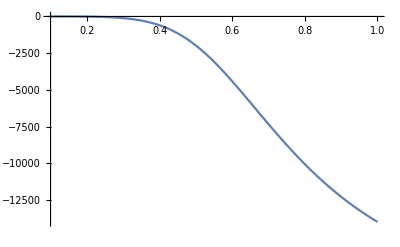

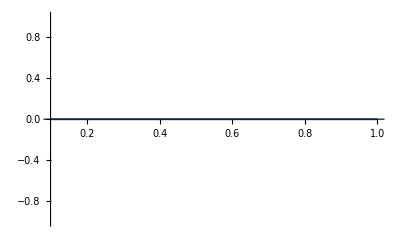

```mathematica
c4=1;
c5= 0;
p=1;
q=0.5;
s=1;
Lambda=L
ConformalH=s1//PowerExpand//Simplify;
Chi = Xs1//PowerExpand//Simplify;
CovariantGalileon={p->1,q->0.5,s->1,φ'[a]->Sqrt[-Chi]/ConformalH,φ''[a]->PhiPP, ℋ[a]-> ConformalH,HconfP->D[ConformalH,a],HconfPP->D[D[ConformalH,a],a]};
LambdaCG=Omega/.DeSitterFP/.ȧ->ConformalH a/.CovariantGalileon/.Subscript[χ, DS]->0.5//PowerExpand//Simplify
LambdaCG/.a->1
LambdaCG/.a->0.1
Plot[Re[LambdaCG],{a,0.1,1}]
Plot[Im[LambdaCG],{a,0.1,1}]
```

```mathematica
ConformalH=s1//PowerExpand//Simplify
Chi = Xs1//PowerExpand//Simplify
Sqrt[-Chi]/ConformalH//PowerExpand//Simplify
PhiPP=D[%,a]//PowerExpand//Simplify
PhiPPP = D[%,a]//PowerExpand//Simplify
```

0.00223607 √((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)

(167331. a^4.)/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))

((0.+182938. ⅈ) a^3.)/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))

((0.-182938. ⅈ) a^3. (30000.+(30000.+9.×10^8 a+1.11998×10^11 a^7)/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))+(0.+548813. ⅈ) a^2. (1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^2

((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)) (((0.+91468.8 ⅈ) a^3. (30000.+9.×10^8 a+1.11998×10^11 a^7) (60000.+1.8×10^9 a+2.23997×10^11 a^7))/((1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)^(3/2))-((0.+1.43421×10^17 ⅈ) a^3. (0.00114798+1. a^6))/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))+(0.+1.09763×10^6 ⅈ) a^1. (1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))-2 (30000.+(30000.+9.×10^8 a+1.11998×10^11 a^7)/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))) ((0.-182938. ⅈ) a^3. (30000.+(30000.+9.×10^8 a+1.11998×10^11 a^7)/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))+(0.+548813. ⅈ) a^2. (1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))))/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^3

DE eq. of state

```mathematica
s1=0.00223606797749979 √(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)
Xs1 = 167330.81007393703 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^2.
s1o5 =Root[-1.680579953429951*^24 a^12+(-1./a^10-150000./a^9-(9.*^9)/a^8-(2.7*^14)/a^7-(4.05*^18)/a^6-(2.43*^22)/a^5) #1^2+(500000./a^8+(6.*^10)/a^7+(2.7*^15)/a^6+(5.4*^19)/a^5+(4.05*^23)/a^4) #1^4+(-(1.*^11)/a^6-(9.*^15)/a^5-(2.7*^20)/a^4-(2.7*^24)/a^3) #1^6+((1.*^16)/a^4+(6.*^20)/a^3+(9.*^24)/a^2) #1^8+(-(5.*^20)/a^2-(1.5*^25)/a) #1^10+1.*^25 #1^12&,2]
Xs1o5 = 10.824004689806106 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^(2/5)
```

0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)

167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2.

Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]

10.824 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(2/5)

```mathematica
(*SubstituteS0 = {H->s0 H0/a, X->XDS Xs0,s->0,p->0,q->0.5, Hdot-> s0 H0 a D[s0 H0/a,a], Xdot->XDS  s0 H0 D[Xs0,a]}*)
SubstituteS1 = {H->s1 H0/a,X->XDS Xs1,s->1,p->1,q->0.5, Hdot-> s1 H0  a D[s1 H0/a,a], Xdot->XDS  s1 H0 a D[Xs1,a]}
SubstituteS1o5 = {H->s1o5 H0/a,X->XDS Xs1o5,s->1/5,p->1,q->5/2, Hdot-> s1 H0  a D[s1o5 H0/a,a], Xdot->XDS  s1o5 H0 a D[Xs1o5,a]}
(*SubstituteS0p5 = {H->s0p5 H0/a, X->XDS Xs0p5,s->0.5,p->0.5,q->0.5, Hdot-> s0p5 H0 a D[s0p5 H0/a,a], Xdot-> XDS s0p5 H0 D[Xs0p5,a]};*)
```

{H→(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a,X→167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2. XDS,s→1,p→1,q→0.5,Hdot→0.00223607 a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0 ((0.00111803 (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3) H0)/(a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))-(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a^2),Xdot→748.326 a (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^1. √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) (-(a (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3))/(2 (1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)^(3/2))+1/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))) H0 XDS}

{H→1/a H0 Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2],X→10.824 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(2/5) XDS,s→1/5,p→1,q→5/2,Hdot→0.00223607 a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0 (-1/a^2 H0 Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]+(H0 (2.0167×10^25 a^11-(10./a^11+(1.35×10^6)/a^10+(7.2×10^10)/a^9+(1.89×10^15)/a^8+(2.43×10^19)/a^7+(1.215×10^23)/a^6) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^2-(-(4.×10^6)/a^9-(4.2×10^11)/a^8-(1.62×10^16)/a^7-(2.7×10^20)/a^6-(1.62×10^24)/a^5) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^4-((6.×10^11)/a^7+(4.5×10^16)/a^6+(1.08×10^21)/a^5+(8.1×10^24)/a^4) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^6-(-(4.×10^16)/a^5-(1.8×10^21)/a^4-(1.8×10^25)/a^3) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^8-((1.×10^21)/a^3+(1.5×10^25)/a^2) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^10))/(a (2 (-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]+4 (500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^3+6 (-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^5+8 ((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^7+10 (-(5.×10^20)/a^2-(1.5×10^25)/a) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^9+1.2×10^26 Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^11))),Xdot→1/((a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(3/5))4.3296 a (-(a (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3))/(2 (1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)^(3/2))+1/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))) H0 XDS Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]}

```mathematica
rhoDE = 120 H^2 χ^2 Subscript[F, 4][χ]-Subscript[G, 2][χ]-6 H^2 Subscript[G, 4][χ]+48 H^2 χ^3 Subscript[F, 4]'[χ]+2 χ Subscript[G, 2]'[χ]-6 √2 H χ^(3/2) Subscript[G, 3]'[χ]+24 H^2 χ Subscript[G, 4]'[χ]+24 H^2 χ^2 Subscript[G, 4]''[χ]
```

120 H^2 X^2 F4[X]-G2[X]-6 H^2 G4[X]+48 H^2 X^3 F4'[X]+2 X G2'[X]-6 √2 H X^(3/2) G3'[X]+24 H^2 X G4'[X]+24 H^2 X^2 G4''[X]

```mathematica
pDE = -24 H^2 χ^2 Subscript[F, 4][χ]-16 Ḣ χ^2 Subscript[F, 4][χ]-32 H χ χ̇ Subscript[F, 4][χ]+Subscript[G, 2][χ]+6 H^2 Subscript[G, 4][χ]+4 Ḣ Subscript[G, 4][χ]-16 H χ^2 χ̇ Subscript[F, 4]'[χ]+√2 √χ χ̇ Subscript[G, 3]'[χ]-12 H^2 χ Subscript[G, 4]'[χ]-8 Ḣ χ Subscript[G, 4]'[χ]-4 H χ̇ Subscript[G, 4]'[χ]-8 H χ χ̇ Subscript[G, 4]''[χ]
```

-24 H^2 X^2 F4[X]-16 Hdot X^2 F4[X]-32 H X Xdot F4[X]+G2[X]+6 H^2 G4[X]+4 Hdot G4[X]-16 H X^2 Xdot F4'[X]+√2 √X Xdot G3'[X]-12 H^2 X G4'[X]-8 Hdot X G4'[X]-4 H Xdot G4'[X]-8 H X Xdot G4''[X]

parametrize functions

```mathematica
c2 =.
c3=.
c4 =.
c5 =.

p =.
q =.
s =.

p2=p;
p3=p+q-1/2;
p4=p+2q;
p5=p+2q-2;

XDS =.

(*this X is for De Felice!!!!*)
XfromMyNotationToNJS = {X->-1/2X,XDS->-1/2XDS,Xdot->-1/2 Xdot}

G2[X]=-c2  X^p2 Hds^2 Subscript[m, p]^2 XDS^-p
G2'[X]=D[G2[X],X];
G2''[X]=D[G2'[X],X];
G3[X]=-c3 X^p3 Hds Subscript[m, p]^2 XDS^(-p-q)
G3'[X]=D[G3[X],X];
G3''[X]=D[G3'[X],X];
G4[X]=-c4 X^p4 XDS^(-p-2 q) Subscript[m, p]^2
Subscript[G, 4]'[X]=D[G4[X],X];
Subscript[G, 4]''[X]=D[ D[G4[X],X],X];
Derivative[3][Subscript[G, 4]][χ]=D[D[ Subscript[G, 4]'[X],X],X];
Subscript[F, 4][X]=c5 X^p5 XDS^(-p-2 q)Subscript[m, p]^2
Subscript[F, 4]'[X]= D[Subscript[F, 4][X],X];
Subscript[F, 4]''[X]=D[Subscript[F, 4]'[X],X];
```

{X→-X/2,XDS→-XDS/2,Xdot→-Xdot/2}

-c2 Hds^2 MPlanck^2 X^p XDS^-p

-c3 Hds MPlanck^2 X^(-1/2+p+q) XDS^(-p-q)

-c4 MPlanck^2 X^(p+2 q) XDS^(-p-2 q)

c5 MPlanck^2 X^(-2+p+2 q) XDS^(-p-2 q)

```mathematica
HdsSubstitution = {Hds-> H0 (OmegaDE0)^(1/(1+s)^2)}
DeSitterFP = {Subscript[c, 2]->3-6 Subscript[c, 4]-24 Subscript[c, 5]+12 Subscript[c, 4] p+24 Subscript[c, 4] q,Subscript[c, 3]->(√2 p)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] p)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] p)/(-1+2 p+2 q)+(8 √2 Subscript[c, 4] p^2)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] q)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] q)/(-1+2 p+2 q)+(24 √2 Subscript[c, 4] p q)/(-1+2 p+2 q)+(16 √2 Subscript[c, 4] q^2)/(-1+2 p+2 q)}
```

{Hds→H0 OmegaDE0^(1/(1+s)^2)}

{c2→3-6 c4-24 c5+12 c4 p+24 c4 q,c3→(√2 p)/(-1+2 p+2 q)-(4 √2 c4 p)/(-1+2 p+2 q)-(16 √2 c5 p)/(-1+2 p+2 q)+(8 √2 c4 p^2)/(-1+2 p+2 q)-(4 √2 c4 q)/(-1+2 p+2 q)-(16 √2 c5 q)/(-1+2 p+2 q)+(24 √2 c4 p q)/(-1+2 p+2 q)+(16 √2 c4 q^2)/(-1+2 p+2 q)}

```mathematica
XDS =.
rhoDE1=rhoDE/.XfromMyNotationToNJS/.HdsSubstitution/.DeSitterFP//Simplify;
pDE1=pDE/.XfromMyNotationToNJS/.HdsSubstitution/.DeSitterFP//Simplify;
OmegaDE0 = 1-OmegaM0-OmegaR0;
wDE =rhoDE1/pDE1//Simplify
```

-((3 X (-8 c5 (H (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-XDS)^q) (H (1+2 p+4 q) (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-1+2 p) (-XDS)^q)+2 c4 (-1+2 p+4 q) (H (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-XDS)^q) (H (1+2 p+4 q) (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-1+2 p) (-XDS)^q)+H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-2 H p (-X)^q+H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-1+2 p) (-XDS)^q) (-XDS)^q))/(-8 c5 (3 H^2 (-X)^(2 q) X+2 Hdot (-X)^(2 q) X+2 H (p+2 q) (-X)^(2 q) Xdot-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (2 p (-X)^q Xdot+2 q (-X)^q Xdot+3 H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) X (-XDS)^q) (-XDS)^q)+2 c4 (-1+2 p+4 q) (3 H^2 (-X)^(2 q) X+2 Hdot (-X)^(2 q) X+2 H (p+2 q) (-X)^(2 q) Xdot-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (2 p (-X)^q Xdot+2 q (-X)^q Xdot+3 H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) X (-XDS)^q) (-XDS)^q)-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (p (-X)^q Xdot+3 H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) X (-XDS)^q) (-XDS)^q))

s  =  0

-0.849994

-0.99899

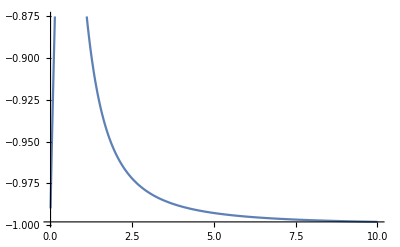

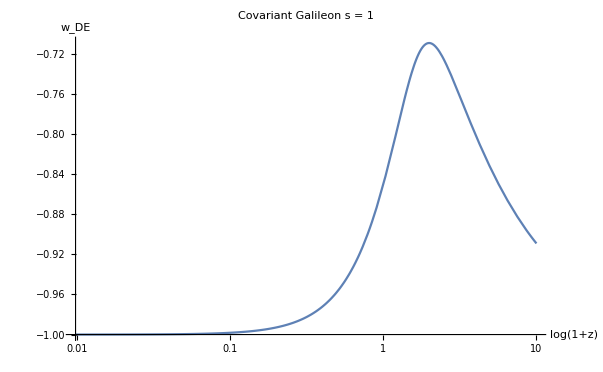

```mathematica
(*OmegaM0=0.3;
OmegaR0=10^(-5);
OmegaDE0 = 1-OmegaM0-OmegaR0;*)

(*XDS =-1;*)

(*c5 = 0;*)

wDEs2 =wDE/.SubstituteS1o5/.OmegaM0-> 0.3/.OmegaR0-> 10^(-5)/.c4-> -1/.c5->100/.XDS->-100/.s->1/5/.p->1/.q->5/2//Simplify;
wDEs1 =wDE/.SubstituteS1/.OmegaM0-> 0.3/.OmegaR0-> 10^(-5)/.c4-> -1/.c5->100/.XDS->-100/.s->1/.p->1/.q->0.5//Simplify;
wDEs1z=%/.a->1/zplus1;
(*rhoDEs0=rhoDE1/.SubstituteS0//PowerExpand//Simplify;
pDEs0=pDE1/.SubstituteS0//PowerExpand//Simplify;
wDEs0 =rhoDEs0/pDEs0/.s->1/.p->1/.q->0.5//Simplify;*)

a=1;
wDEs1
a=0.0010;
wDEs1
a=.


Plot[Re[wDEs1],{a,0.01,10}]
LogLinearPlot[Re[wDEs1z],{zplus1,0,10}, AxesLabel->{Style["log(1+z)",FontSize->20],Style["w_DE",FontSize->20]},PlotLabel->Style["Covariant Galileon s = 1", FontSize->25]]
```

-0.850347

-0.999439

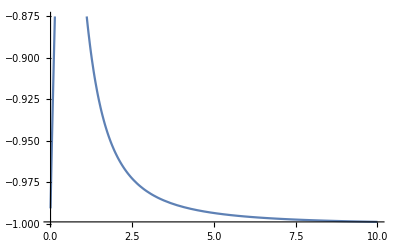

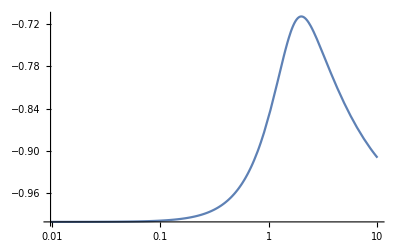

```mathematica
OmegaM0=0.3;
OmegaR0=10^(-4);
OmegaDE0 = 1-OmegaM0-OmegaR0;

(*XDS =-1;*)
c4 =20;
c5 = 0;


wDEs12 =wDE/.SubstituteS1/.XDS->-1/.s->1/.p->1/.q->0.5//Simplify;

(*rhoDEs0=rhoDE1/.SubstituteS0//PowerExpand//Simplify;
pDEs0=pDE1/.SubstituteS0//PowerExpand//Simplify;
wDEs0 =rhoDEs0/pDEs0/.s->1/.p->1/.q->0.5//Simplify;*)

a=1;
wDEs12
a=0.0010;
wDEs12
a=.

wDEs1z2=wDEs12/.a->1/zplus1;
Plot[Re[wDEs12],{a,0.01,10}]
LogLinearPlot[Re[wDEs1z2],{zplus1,0,10}]
c4=.
```

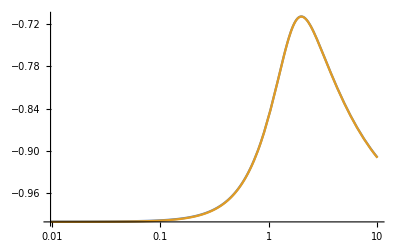

```mathematica
LogLinearPlot[{Re[wDEs1z],Re[wDEs1z2]},{zplus1,0,10}]
```

```mathematica
OmegaM0=.
OmegaR0=.
OmegaDE0=.
c4=.
```

```mathematica
XDS
```

-1

```mathematica
SubstituteS1
```

{H→(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a,X→167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2. XDS,s→1,p→1,q→0.5,Hdot→0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0 ((0.00111803 (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3) H0)/(a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))-(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a^2),Xdot→748.326 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^1. √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) (-(a (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3))/(2 (1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)^(3/2))+1/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))) H0 XDS}